```mathematica
DataToAssociation[filename_] := 
Module[{},
data = Import[FileNameJoin[{NotebookDirectory[], filename}],"Table"];
transpose = Transpose[data];
timeData=Transpose[Rest[transpose]/. minutes_Integer:>TimeObject[{Quotient[minutes,100],Mod[minutes,100],0}]];
timeDiffTable = Table[Table[timeData[[All,j]][[i]]-timeData[[All,j]][[i-1]], {i, 2, Length[timeData]}], {j, 1, Length[Transpose[timeData]]}];
maxModeTimes = Table[Max[Commonest[timeDiffTable[[All, i]]]], {i, 1, Length[timeDiffTable[[1]]]}];
stopPairs = Table[List[First[transpose][[i-1]],First[transpose][[i]]], {i, 2, Length[maxModeTimes]+1}];
association = Association[Table[stopPairs[[i]]->maxModeTimes[[i]], {i, 1, Length[stopPairs]}]];
waiting = Association[Table[Keys[association][[i]]->
If[
(StringTake[Keys[association][[i]][[1]], -4] == "_arr" && StringTake[Keys[association][[i]][[2]], -4] == "_dep") ,
association[[Key[Keys[association][[i]]]]], Quantity[0, "Minutes"]],
{i, 1, Length[Keys[association]]}]];
travelTimeAssociation = Module[{cleaned},
cleaned = Association[];
i = 0;
While[i <Length[association],
i++;
If[waiting[[i]]==0 Quantity[, "Minutes"] && (StringTake[Keys[association][[i]][[1]], -4] == "_dep" || StringTake[Keys[association][[i]][[2]], -4] == "_arr"),
If[StringTake[Keys[association][[i]][[1]], -4] == "_dep",
AppendTo[cleaned, List[StringDrop[Keys[association][[i]][[1]], -4],Keys[association][[i]][[2]]]-> association[[Key[Keys[association][[i]]]]]],
AppendTo[cleaned, List[Keys[association][[i]][[1]],StringDrop[Keys[association][[i]][[2]], -4]]-> association[[Key[Keys[association][[i]]]]]]
],
If [waiting[[i]]==0 Quantity[, "Minutes"],
cleaned[Keys[association][[i]]] = association[[Key[Keys[association][[i]]]]],
Nothing[]],
Nothing[]];
];
cleaned
];

allStops = List[];
AppendTo[allStops, Keys[travelTimeAssociation][[1]][[1]]];
Do[AppendTo[allStops, x[[2]]],
{x, Keys[travelTimeAssociation]}
];
(*List[travelTimeAssociation, waiting, allStops]*)
travelTimeAssociation
];

SharedStops[route1_, route2_] := Intersection[Stops[route1], Stops[route2]];
```

```mathematica
x_⊕y_:=Max[x,y]
```

```mathematica
x_ ⊗y_:=x+y
```

```mathematica
mplus[x_,y_]:=MapThread[Max,{x,y}, 2]
```

```mathematica
mtimes[x_,y_]:=Inner[Plus,x,y,Max]
```

```mathematica
mpower[x_,p_]:= Module[{res},
If[p>=1,
res = x,
res = EMatrix[Length[x]]];
For[i = 2, i<=p, i++,
res = mtimes[res, x]
];
res
]
```

```mathematica
scalarplus[x_,y_]:=Outer[Max,{x},y]
```

```mathematica
eps=-Infinity
```

-∞

```mathematica
EpsilonMatrix[n_] := Table[Table[eps, {col, 1, n}], {row, 1, n}]
(* Returns an n x n matrix filled with Epsilon *)
```

```mathematica
EMatrix[n_]:= Table[Table[If[col == row, 0, eps], {col, 1, n}], {row, 1, n}]
(* Returns an n x n identity matrix *)
```

```mathematica
MakeNicePlaceName[rn_, s1_, s2_] :=ToString[StringJoin["p:",rn,":", s1, "+", s2]]
(* returns a formatted place name *)
```

```mathematica
MakeNiceTransitionName[rn_,q_] := ToString[StringJoin["q:",rn,":", q]]
(* returns a formatted transition name *)
```

```mathematica
MergeDirections[forward_, reverse_] := Module[{f, r, merged, nk, xS, start, end},
(* merges the forward and backward (arbitary) directions of a bus route *)
f = DataToAssociation[forward];
start = Keys[f][[1]][[1]];
r = DataToAssociation[reverse];
end = Keys[r][[1]][[1]];

Do[
nk ={StringJoin[x[[1]], If[x[[1]] ==start,"_end","_fwd"]], StringJoin[x[[2]], If[x[[2]] ==end,"_end","_fwd"]]};
f[nk] = f[x];
f[x] =.,
{x, Keys[f]}
];

Do[
nk ={StringJoin[x[[1]], If[x[[1]] ==end,"_end","_rev"]],StringJoin[x[[2]],  If[x[[2]] ==start,"_end","_rev"]]};
r[nk] = r[x];
r[x] =.,
{x, Keys[r]}
];

merged = Join[f, r];
merged
]
```

```mathematica
GetTransitionStopName[transitionString_] := StringDrop[StringSplit[transitionString, ":"][[-1]],-4];
(* returns the transition name from a "nice" formatted transition *)

GetTransitionStop[transitionString_]:=StringSplit[transitionString, ":"][[-1]];
(* returns the transition stop, including route direction from a "nice" formatted transition *)
```

```mathematica
GetTransitionRoute[transitionString_] :=StringSplit[transitionString, ":"][[2]];(* returns the transition route number from a "nice" formatted transition *)
```

```mathematica
Algorithm821[lineDataFile_, routeNumbers_]:=
(*Line data file is a list of associations, where each asscoiation corresponds to a merged version of the TT association for the forward and backward journey of a given route. So each association represents a route*)
Module[{TAPsFromRoute, Synchronization, NumberRoutes, cycleTime},
cycleTime =10 Quantity[, "Minutes"];

NumberRoutes[] := Module[{indexedAssociations},
(* returns an association with route number as key and travel time associations (route data) as values *)
indexedAssociations = Association[];
For[i=1,i<=Length[routeNumbers], i++,
indexedAssociations[routeNumbers[[i]]]= lineDataFile[[i]];
];
indexedAssociations
];

TAPsFromRoute[routeNumber_, routeAssociation_] :=Module[{startStop, endStop, cumulativeTime,nextStopCumulativeTime, modCumulative, modNextCumulative,tokens, finalHoldingTime, transitions, places, arcs},
(* returns the transitions, arcs, and place of an individual route *)
transitions = List[];
places = Association[];
arcs = List[];
startStop = Keys[routeAssociation][[1]][[1]];
endStop = Keys[routeAssociation][[-1]][[1]];
AppendTo[transitions,MakeNiceTransitionName[routeNumber, startStop]];
cumulativeTime = 0 Quantity[, "Minutes"];
Do[
AppendTo[transitions,MakeNiceTransitionName[routeNumber, pair[[2]]]];
nextStopCumulativeTime =cumulativeTime + routeAssociation[[Key[pair]]];
modCumulative = Mod[cumulativeTime, cycleTime];
modNextCumulative = Mod[nextStopCumulativeTime, cycleTime];
tokens = Ceiling[(routeAssociation[[Key[pair]]] + modCumulative - modNextCumulative)/cycleTime];
AppendTo[places,  MakeNicePlaceName[routeNumber, pair[[1]],pair[[2]]]->List[routeAssociation[[Key[pair]]], tokens]];
cumulativeTime = nextStopCumulativeTime;
AppendTo[arcs, MakeNiceTransitionName[routeNumber, pair[[1]]]->Keys[places][[-1]]];
AppendTo[arcs, Keys[places][[-1]]->MakeNiceTransitionName[routeNumber, pair[[2]]]];
,
{pair, Keys[routeAssociation][[1;;-2]]}
];
finalHoldingTime =routeAssociation[[Key[List[endStop, StringReplace[startStop, {"fwd"->"rev"}]]]]];
nextStopCumulativeTime =cumulativeTime + finalHoldingTime;
modCumulative = Mod[cumulativeTime, cycleTime];
modNextCumulative = Mod[nextStopCumulativeTime, cycleTime];
tokens = Ceiling[(finalHoldingTime + modCumulative - modNextCumulative)/cycleTime];
AppendTo[places, MakeNicePlaceName[routeNumber,endStop, startStop]->List[finalHoldingTime, tokens] ]; (*make sure this is indeed the last one*)
AppendTo[arcs, MakeNiceTransitionName[routeNumber, endStop]->MakeNicePlaceName[routeNumber, endStop, startStop]];
AppendTo[arcs, MakeNicePlaceName[routeNumber, endStop, startStop]->MakeNiceTransitionName[routeNumber, startStop]];
List[transitions, arcs, places]
];

Synchronization[routePlaces_] := Module[{arcs, places, indexedRoutes},
(* returns the arcs and places between routes with shared stops *)
indexedRoutes = NumberRoutes[];
arcs=List[];
places=Association[];
Do[
Do[
Do[
Do[
If[assoc1 != assoc2,
If[StringDrop[key1[[2]],-4]==StringDrop[key2[[2]],-4],
(* add arc from previous stop on origin line to new place *)
(* add arc from new place to shared stop on the other line *)
placeWeWant = MakeNicePlaceName[assoc2, key2[[1]], key2[[2]] ];
AppendTo[places, MakeNicePlaceName[StringJoin[assoc2, "->", assoc1], key2[[1]], key1[[2]]]->routePlaces[[placeWeWant]]];
AppendTo[arcs, MakeNiceTransitionName[assoc2,key2[[1]]]->Keys[places][[-1]]];
AppendTo[arcs, Keys[places][[-1]]->MakeNiceTransitionName[assoc1, key1[[2]]]];,
Nothing[]
];
Nothing[]
];,
{key2,Keys[indexedRoutes[[Key[assoc2]]]]}
],
{key1,Keys[indexedRoutes[[Key[assoc1]]]]}
],
{assoc2,Keys[indexedRoutes]}
],
{assoc1,Keys[indexedRoutes]}
];
List[arcs, places]
];

transitions = List[];
places = Association[];
arcs = List[];

(* find transitions, arcs, and places for all routes *);
For[i=1, i<=Length[lineDataFile], i++,
temps= TAPsFromRoute[routeNumbers[[i]], lineDataFile[[i]]];
transitions = Join[transitions, temps[[1]]];
arcs = Join[arcs, temps[[2]]];
places = Join[places, temps[[3]]];
];

(* find arcs and places between routes *);
sync = Synchronization[places];
arcs = Join[arcs, sync[[1]]];
places = Join[places, sync[[2]]];

List[transitions, arcs, places]
]
```

```mathematica
MatrixFromPetriNet[transitions_, arcs_, places_] := Module[{AMatrices, GetPlaceBetween, A0Star, MatrixABlocks, ATwiddle},
(*reccurence relation*)
GetPlaceBetween[t1_, t2_] :=Module[{p},
If[
GetTransitionRoute[t1]==GetTransitionRoute[t2],

p =MakeNicePlaceName[GetTransitionRoute[t1], GetTransitionStop[t1], GetTransitionStop[t2]],

p = MakeNicePlaceName[StringJoin[GetTransitionRoute[t1], "->", GetTransitionRoute[t2]], GetTransitionStop[t1], GetTransitionStop[t2]]
];
p
];

AMatrices[]:=Module[{maxTokens, p, row, matrix, matrices},
maxTokens = 0;
Do[
If[x[[2]]>maxTokens,
maxTokens=x[[2]],
Nothing[]
],
{x, places}];

matrices = List[];

For[m=0, m<=maxTokens, m++, 
matrix = List[];
Do[
row =List[];
Do[
p =GetPlaceBetween[j,i];
If[MemberQ[Keys[places], p],
p = places[[p]];
If[p[[2]]==m,
AppendTo[row, (p[[1]]/Quantity[, "Minutes"])],
AppendTo[row, eps ]
],
AppendTo[row, eps ];
];,
{j, transitions}];
AppendTo[matrix, row];
,
{i, transitions}];
AppendTo[matrices, matrix];
];
matrices
];

A0Star[A0_] :=Module[{R},
R =EMatrix[Length[A0]];
For[l=1, l<=Length[transitions], l=l+1,
R=mplus[R,mpower[A0, l]];
];
R
];

MatrixABlocks[ AMatrixList_, A0S_] :=Module[{s, blocks, a},
blocks = List[];
Do[
a= mtimes[A0S, A];
AppendTo[blocks,a],
{A, Drop[AMatrixList, 1]}
];
blocks
];

ATwiddle[blocks_]:=Module[{atwid, flatBlocks, row, rows, blockLen},
If[Length[blocks]==1,
atwid = blocks[[1]],
blockLen = Length[blocks[[1]]];
flatBlocks = ArrayFlatten[{blocks}];
rows=flatBlocks;
For [i=1, i<=Length[blocks],i++,
row =Table[EpsilonMatrix[blockLen], Length[blocks]];
row =ReplacePart[row, i->EMatrix[blockLen]];
rows =Join[rows,row, 1];
Print["hello"];
];
atwid =rows;
];
atwid
];

Comp[]:=Module[{matrixList, A0S, matrixABlocks, matrix},
matrixList = AMatrices[];
A0S = A0Star[matrixList[[1]]];
matrixABlocks = MatrixABlocks[matrixList, A0S];
matrix = ATwiddle[matrixABlocks];

matrix
];
Comp[]
]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"]
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"]
```

<|{Wallacebrae_Road_end,Bodachra_Place_fwd}→7. min,{Bodachra_Place_fwd,North_Donside_Road_fwd}→7. min,{North_Donside_Road_fwd,School_Road_fwd}→7. min,{School_Road_fwd,Errol_Street_fwd}→5. min,{Errol_Street_fwd,Castle_Street_fwd}→5. min,{Castle_Street_fwd,Music_Hall_fwd}→5. min,{Music_Hall_fwd,Bridge_of_Dee_Court_end}→14. min,{Bridge_of_Dee_Court_end,Robert_Gordon_University_rev}→4. min,{Robert_Gordon_University_rev,Auchinyell_Gardens_rev}→8. min,{Auchinyell_Gardens_rev,Great_Western_Road_rev}→8. min,{Great_Western_Road_rev,Castle_Street_rev}→11. min,{Castle_Street_rev,Errol_Street_rev}→4. min,{Errol_Street_rev,School_Drive_rev}→5. min,{School_Drive_rev,Fraserfield_Gardens_rev}→7. min,{Fraserfield_Gardens_rev,Wallacebrae_Road_end}→13. min|>

<|{Golf_Links_end,Beach_Boulevard_fwd}→10. min,{Beach_Boulevard_fwd,St_Andrew's_Cathedral_fwd}→10. min,{St_Andrew's_Cathedral_fwd,Prince_Arthur_Street_fwd}→13. min,{Prince_Arthur_Street_fwd,Mastrick_Shops_fwd}→15. min,{Mastrick_Shops_fwd,Turning_Circle_end}→9. min,{Turning_Circle_end,Summerhill_Terrace_rev}→15. min,{Summerhill_Terrace_rev,Bridge_Street_rev}→15. min,{Bridge_Street_rev,Castle_Street_rev}→7. min,{Castle_Street_rev,Beach_Boulevard_rev}→6. min,{Beach_Boulevard_rev,Golf_Links_end}→14. min|>

```mathematica
TAPs=Algorithm821[{b1, b13}, {"1", "13"}]
```

{{q:1:Wallacebrae_Road_end,q:1:Bodachra_Place_fwd,q:1:North_Donside_Road_fwd,q:1:School_Road_fwd,q:1:Errol_Street_fwd,q:1:Castle_Street_fwd,q:1:Music_Hall_fwd,q:1:Bridge_of_Dee_Court_end,q:1:Robert_Gordon_University_rev,q:1:Auchinyell_Gardens_rev,q:1:Great_Western_Road_rev,q:1:Castle_Street_rev,q:1:Errol_Street_rev,q:1:School_Drive_rev,q:1:Fraserfield_Gardens_rev,q:13:Golf_Links_end,q:13:Beach_Boulevard_fwd,q:13:St_Andrew's_Cathedral_fwd,q:13:Prince_Arthur_Street_fwd,q:13:Mastrick_Shops_fwd,q:13:Turning_Circle_end,q:13:Summerhill_Terrace_rev,q:13:Bridge_Street_rev,q:13:Castle_Street_rev,q:13:Beach_Boulevard_rev},{q:1:Wallacebrae_Road_end→p:1:Wallacebrae_Road_end+Bodachra_Place_fwd,p:1:Wallacebrae_Road_end+Bodachra_Place_fwd→q:1:Bodachra_Place_fwd,q:1:Bodachra_Place_fwd→p:1:Bodachra_Place_fwd+North_Donside_Road_fwd,p:1:Bodachra_Place_fwd+North_Donside_Road_fwd→q:1:North_Donside_Road_fwd,q:1:North_Donside_Road_fwd→p:1:North_Donside_Road_fwd+School_Road_fwd,p:1:North_Donside_Road_fwd+School_Road_fwd→q:1:School_Road_fwd,q:1:School_Road_fwd→p:1:School_Road_fwd+Errol_Street_fwd,p:1:School_Road_fwd+Errol_Street_fwd→q:1:Errol_Street_fwd,q:1:Errol_Street_fwd→p:1:Errol_Street_fwd+Castle_Street_fwd,p:1:Errol_Street_fwd+Castle_Street_fwd→q:1:Castle_Street_fwd,q:1:Castle_Street_fwd→p:1:Castle_Street_fwd+Music_Hall_fwd,p:1:Castle_Street_fwd+Music_Hall_fwd→q:1:Music_Hall_fwd,q:1:Music_Hall_fwd→p:1:Music_Hall_fwd+Bridge_of_Dee_Court_end,p:1:Music_Hall_fwd+Bridge_of_Dee_Court_end→q:1:Bridge_of_Dee_Court_end,q:1:Bridge_of_Dee_Court_end→p:1:Bridge_of_Dee_Court_end+Robert_Gordon_University_rev,p:1:Bridge_of_Dee_Court_end+Robert_Gordon_University_rev→q:1:Robert_Gordon_University_rev,q:1:Robert_Gordon_University_rev→p:1:Robert_Gordon_University_rev+Auchinyell_Gardens_rev,p:1:Robert_Gordon_University_rev+Auchinyell_Gardens_rev→q:1:Auchinyell_Gardens_rev,q:1:Auchinyell_Gardens_rev→p:1:Auchinyell_Gardens_rev+Great_Western_Road_rev,p:1:Auchinyell_Gardens_rev+Great_Western_Road_rev→q:1:Great_Western_Road_rev,q:1:Great_Western_Road_rev→p:1:Great_Western_Road_rev+Castle_Street_rev,p:1:Great_Western_Road_rev+Castle_Street_rev→q:1:Castle_Street_rev,q:1:Castle_Street_rev→p:1:Castle_Street_rev+Errol_Street_rev,p:1:Castle_Street_rev+Errol_Street_rev→q:1:Errol_Street_rev,q:1:Errol_Street_rev→p:1:Errol_Street_rev+School_Drive_rev,p:1:Errol_Street_rev+School_Drive_rev→q:1:School_Drive_rev,q:1:School_Drive_rev→p:1:School_Drive_rev+Fraserfield_Gardens_rev,p:1:School_Drive_rev+Fraserfield_Gardens_rev→q:1:Fraserfield_Gardens_rev,q:1:Fraserfield_Gardens_rev→p:1:Fraserfield_Gardens_rev+Wallacebrae_Road_end,p:1:Fraserfield_Gardens_rev+Wallacebrae_Road_end→q:1:Wallacebrae_Road_end,q:13:Golf_Links_end→p:13:Golf_Links_end+Beach_Boulevard_fwd,p:13:Golf_Links_end+Beach_Boulevard_fwd→q:13:Beach_Boulevard_fwd,q:13:Beach_Boulevard_fwd→p:13:Beach_Boulevard_fwd+St_Andrew's_Cathedral_fwd,p:13:Beach_Boulevard_fwd+St_Andrew's_Cathedral_fwd→q:13:St_Andrew's_Cathedral_fwd,q:13:St_Andrew's_Cathedral_fwd→p:13:St_Andrew's_Cathedral_fwd+Prince_Arthur_Street_fwd,p:13:St_Andrew's_Cathedral_fwd+Prince_Arthur_Street_fwd→q:13:Prince_Arthur_Street_fwd,q:13:Prince_Arthur_Street_fwd→p:13:Prince_Arthur_Street_fwd+Mastrick_Shops_fwd,p:13:Prince_Arthur_Street_fwd+Mastrick_Shops_fwd→q:13:Mastrick_Shops_fwd,q:13:Mastrick_Shops_fwd→p:13:Mastrick_Shops_fwd+Turning_Circle_end,p:13:Mastrick_Shops_fwd+Turning_Circle_end→q:13:Turning_Circle_end,q:13:Turning_Circle_end→p:13:Turning_Circle_end+Summerhill_Terrace_rev,p:13:Turning_Circle_end+Summerhill_Terrace_rev→q:13:Summerhill_Terrace_rev,q:13:Summerhill_Terrace_rev→p:13:Summerhill_Terrace_rev+Bridge_Street_rev,p:13:Summerhill_Terrace_rev+Bridge_Street_rev→q:13:Bridge_Street_rev,q:13:Bridge_Street_rev→p:13:Bridge_Street_rev+Castle_Street_rev,p:13:Bridge_Street_rev+Castle_Street_rev→q:13:Castle_Street_rev,q:13:Castle_Street_rev→p:13:Castle_Street_rev+Beach_Boulevard_rev,p:13:Castle_Street_rev+Beach_Boulevard_rev→q:13:Beach_Boulevard_rev,q:13:Beach_Boulevard_rev→p:13:Beach_Boulevard_rev+Golf_Links_end,p:13:Beach_Boulevard_rev+Golf_Links_end→q:13:Golf_Links_end,q:13:Bridge_Street_rev→p:13->1:Bridge_Street_rev+Castle_Street_fwd,p:13->1:Bridge_Street_rev+Castle_Street_fwd→q:1:Castle_Street_fwd,q:13:Bridge_Street_rev→p:13->1:Bridge_Street_rev+Castle_Street_rev,p:13->1:Bridge_Street_rev+Castle_Street_rev→q:1:Castle_Street_rev,q:1:Errol_Street_fwd→p:1->13:Errol_Street_fwd+Castle_Street_rev,p:1->13:Errol_Street_fwd+Castle_Street_rev→q:13:Castle_Street_rev,q:1:Great_Western_Road_rev→p:1->13:Great_Western_Road_rev+Castle_Street_rev,p:1->13:Great_Western_Road_rev+Castle_Street_rev→q:13:Castle_Street_rev},<|p:1:Wallacebrae_Road_end+Bodachra_Place_fwd→{7. min,0},p:1:Bodachra_Place_fwd+North_Donside_Road_fwd→{7. min,1},p:1:North_Donside_Road_fwd+School_Road_fwd→{7. min,1},p:1:School_Road_fwd+Errol_Street_fwd→{5. min,0},p:1:Errol_Street_fwd+Castle_Street_fwd→{5. min,1},p:1:Castle_Street_fwd+Music_Hall_fwd→{5. min,0},p:1:Music_Hall_fwd+Bridge_of_Dee_Court_end→{14. min,2},p:1:Bridge_of_Dee_Court_end+Robert_Gordon_University_rev→{4. min,0},p:1:Robert_Gordon_University_rev+Auchinyell_Gardens_rev→{8. min,1},p:1:Auchinyell_Gardens_rev+Great_Western_Road_rev→{8. min,1},p:1:Great_Western_Road_rev+Castle_Street_rev→{11. min,1},p:1:Castle_Street_rev+Errol_Street_rev→{4. min,0},p:1:Errol_Street_rev+School_Drive_rev→{5. min,1},p:1:School_Drive_rev+Fraserfield_Gardens_rev→{7. min,0},p:1:Fraserfield_Gardens_rev+Wallacebrae_Road_end→{13. min,2},p:13:Golf_Links_end+Beach_Boulevard_fwd→{10. min,1},p:13:Beach_Boulevard_fwd+St_Andrew's_Cathedral_fwd→{10. min,1},p:13:St_Andrew's_Cathedral_fwd+Prince_Arthur_Street_fwd→{13. min,2},p:13:Prince_Arthur_Street_fwd+Mastrick_Shops_fwd→{15. min,2},p:13:Mastrick_Shops_fwd+Turning_Circle_end→{9. min,1},p:13:Turning_Circle_end+Summerhill_Terrace_rev→{15. min,2},p:13:Summerhill_Terrace_rev+Bridge_Street_rev→{15. min,2},p:13:Bridge_Street_rev+Castle_Street_rev→{7. min,1},p:13:Castle_Street_rev+Beach_Boulevard_rev→{6. min,1},p:13:Beach_Boulevard_rev+Golf_Links_end→{14. min,1},p:13->1:Bridge_Street_rev+Castle_Street_fwd→{7. min,1},p:13->1:Bridge_Street_rev+Castle_Street_rev→{7. min,1},p:1->13:Errol_Street_fwd+Castle_Street_rev→{5. min,1},p:1->13:Great_Western_Road_rev+Castle_Street_rev→{11. min,1}|>}

```mathematica
mtx =MatrixFromPetriNet[TAPs[[1]], TAPs[[2]], TAPs[[3]]]
```

2

2

hello

hello

{{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,13.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,20.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,7.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,7.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,12.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,5.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,7.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,10.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,12.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,14.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,18.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,8.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,8.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,11.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,7.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,15.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,11.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,5.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,12.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,14.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,10.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,10.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,13.,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,15.,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,9.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,15.,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,15.,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,5.,-∞,-∞,-∞,-∞,-∞,11.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,7.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,6.,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{{0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0}},{{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞}},{{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞}},{{0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,0}}}

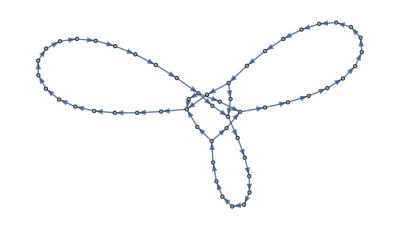

```mathematica
Graph[TAPs[[2]]]
```

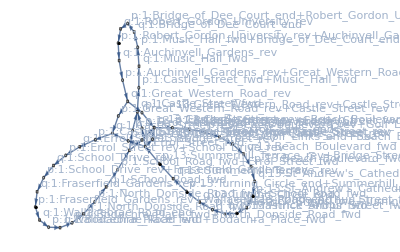

```mathematica
placesList=Keys[TAPs[[3]]];
transitionsList=TAPs[[1]];
arcsList=TAPs[[2]];
initialMarkings=#[[2]]&/@Values[TAPs[[3]]];
petriNet=ResourceFunction["MakePetriNet"][placesList,transitionsList,arcsList, initialMarkings];
petriNet["LabeledGraph"]
```